```mathematica
Graph[{
even->odd,
even->even,
odd->even
}]
```

-Graphics-

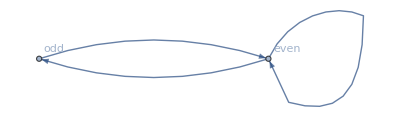

```mathematica
Graph[{
even->odd,
even->even,
odd->even
},VertexLabels->"Name"]
```

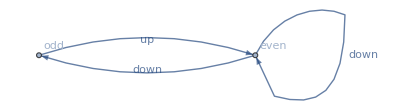

```mathematica
Graph[{
even->odd,
even->even,
odd->even
},VertexLabels->"Name", EdgeLabels->{
(even->odd)->down,
(even->even)->down,
(odd->even)->up
}]
```

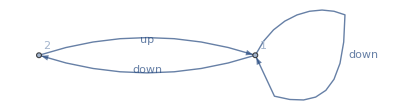

```mathematica
IndexGraph[%3]
```

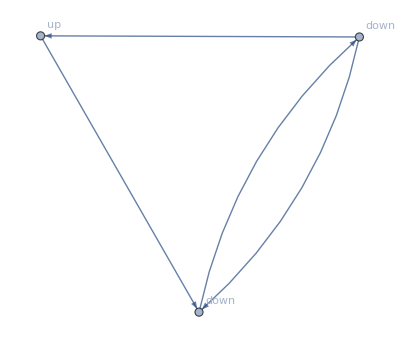

```mathematica
LineGraph[Graph[{1, 2}, {DirectedEdge[1, 2], DirectedEdge[1, 1], DirectedEdge[2, 1]}, {EdgeLabels -> {DirectedEdge[2, 1] -> up, DirectedEdge[1, 1] -> down, DirectedEdge[1, 2] -> down}, VertexLabels -> {"Name"}}]]
```

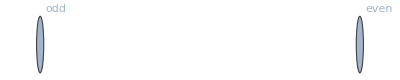

```mathematica
GraphComplement[%3]
```

```mathematica
FindHamiltonianCycle[%3]
```

{{even->odd,odd->even}}

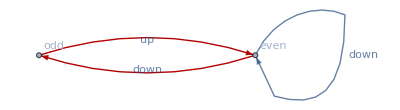

```mathematica
HighlightGraph[Graph[{even,odd},{{{1,2},{1,1},{2,1}},Null},{EdgeLabels->{odd->even->up,even->odd->down,even->even->down},VertexLabels->{"Name"}}],{{even->odd,odd->even}}]
```

```mathematica
FindEulerianCycle[%3]
```

{{even->even,even->odd,odd->even}}

```mathematica
WeightedGraphQ[%3]
```

False

```mathematica
UndirectedGraphQ[%3]
```

False

```mathematica
UndirectedGraphQ[%3]
```

False

```mathematica
LoopFreeGraphQ[%3]
```

False

```mathematica
SimpleGraphQ[%3]
```

False

```mathematica
HamiltonianGraphQ[%3]
```

True

```mathematica
EmptyGraphQ[%3]
```

False

```mathematica
DirectedGraphQ[%3]
```

True

```mathematica
ConnectedGraphQ[%3]
```

True

```mathematica
CompleteGraphQ[%3]
```

False

```mathematica
AcyclicGraphQ[%3]
```

False

```mathematica
n/2>3(n/2)+1
```

n/2>1+(3 n)/2

```mathematica
Reduce[n/2>1+(3 n)/2]
```

n<-1

```mathematica
ExpandAll[3(n/2)+1]
```

1+(3 n)/2

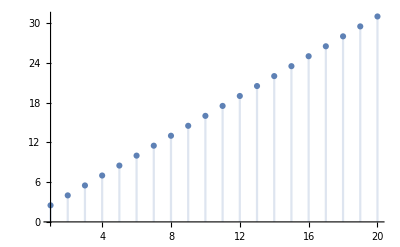

```mathematica
DiscretePlot[1+(3 n)/2,{n,1,20}]
```

```mathematica
(n/2>3(n/2)+1)∧n∈
```

n/2>1+(3 n)/2&&n∈ℤ&&n>0

```mathematica
Reduce[n/2>1+(3 n)/2&&n∈Integers&&n>0]
```

False

```mathematica
Reduce[n/2<1+(3 n)/2&&n∈Integers&&n>0]
```

n∈ℤ&&n≥1

```mathematica
Reduce[n/2==1+(3 n)/2&&n∈Integers&&n>0]
```

False

```mathematica
Reduce[n/2≥1+(3 n)/2&&n∈Integers&&n>0]
```

False

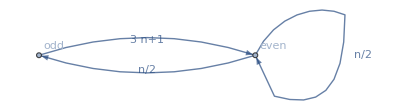

```mathematica
Graph[{
even->odd,
even->even,
odd->even
},VertexLabels->"Name", EdgeLabels->{
(even->odd)->n/2,
(even->even)->n/2,
(odd->even)->3n+1
}]
```

```mathematica
f@x
```

f[x]

```mathematica
x//f
```

f[x]

```mathematica
f[n_Integer]:=n
```

```mathematica
f[4]
```

4

```mathematica
f[4.43]
```

f[4.43]

```mathematica
even[n]
```

even[n]

```mathematica
g[n_PositiveInteger]:=n
```

```mathematica
g[4]
```

g[4]

```mathematica
h[n_Prime]:=n
```

```mathematica
h[4]
```

h[4]

```mathematica
h[5]
```

h[5]

```mathematica
n_Integer/;n>1
```

n_Integer/;n>1

```mathematica
bb[n_Integer/;n>1]:=n
```

```mathematica
bb[34]
```

34

```mathematica
bb[-2]
```

bb[-2]

```mathematica
bb[0]
```

bb[0]

```mathematica
bb[43.4334]
```

bb[43.4334]

```mathematica
Head[3]
```

Integer

```mathematica
FullForm[3]
```

3

```mathematica
Integer[3]
```

Integer[3]

```mathematica
Integer[3]+12
```

12+Integer[3]

```mathematica
(3n+1)/2
```

1/2 (1+3 n)

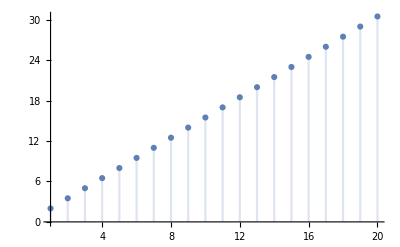

```mathematica
DiscretePlot[1/2 (1+3 n),{n,1,20}]
```

```mathematica
3(n/2)+1
```

1+(3 n)/2

```mathematica
DiscretePlot[1+(3 n)/2,{n,1,20}]
```

-Graphics-

```mathematica
ClearAll[f]
```

```mathematica
f[a]+f[b]/.f[x_]->x^2
```

a^2+b^2

```mathematica
f[a]+f[b]+f[c]/.f[x_]->x^2
```

a^2+b^2+c^2

```mathematica
f[a]+f[b]+f[a+b]/.f[x_]->x^2
```

a^2+b^2+(a+b)^2

```mathematica
f[a]+f[b]+f[a+c]/.f[x_]->x^2
```

a^2+b^2+(a+c)^2

```mathematica
f[a]+f[b]+f[f[a+c]]/.f[x_]->x^2
```

a^2+b^2+f[a+c]^2

```mathematica
f[a]+f[b]+f[f[a+c]]/.f[_]->x^2
```

3 x^2

```mathematica
22/7
```

22/7

```mathematica
N[22/7]
```

3.14286

```mathematica
N[22/7,100]
```

3.142857142857142857142857142857142857142857142857142857142857142857142857142857142857142857142857143